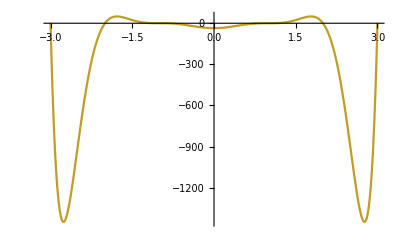

```mathematica
F=(x+3)(x+2)(x+1)^3(x-1)^3(x-2)(x-3);
Plot[F,{x,-3,3}]
```

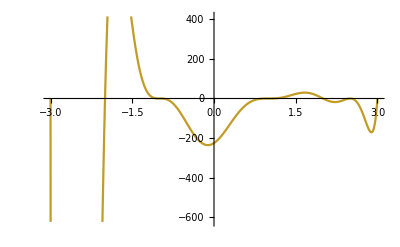

```mathematica
F2=(x+3)(x+2)(x+1)^3(x-1)^3(x-2)(x-(2+3)/2)^2(x-3);
Plot[F2,{x,-3,3}]
```

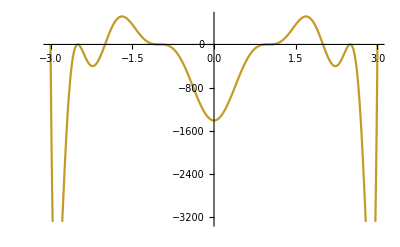

```mathematica
F3=(x+3)(x-(-2-3)/2)^2(x+2)(x+1)^3(x-1)^3(x-2)(x-(2+3)/2)^2(x-3);
Plot[F3,{x,-3,3}]
```

```mathematica
Reduce[F≥0,x]
FindMinimum[{F,-3≤x≤-2},x]
FindMinimum[{F,-1≤x≤1},x]
FindMinimum[{F,2≤x≤3},x]
```

x≤-3||-2≤x≤-1||1≤x≤2||x≥3

{-1449.34,{x→-2.76172}}

{-36.,{x→-2.94297×10^-17}}

{-1449.34,{x→2.76172}}